#### Problem 10.6.22b

```mathematica
f[x_,t_]:=(-(x^2)/10)+2*x+Sum[(160*(Cos[n*Pi]-1)/((n*Pi)^3))*Exp[-((n*Pi/20)^2)*t]*Sin[n*Pi*x/20], {n,50}]
```

```mathematica
v[x_]:=(-(x^2)/10)+2*x
```

```mathematica
u1[x_]:=(-(x^2)/10)+2*x+Sum[(160*(Cos[n*Pi]-1)/((n*Pi)^3))*Exp[-((n*Pi/20)^2)*0]*Sin[n*Pi*x/20], {n,50}]
```

```mathematica
u2[x_]:=(-(x^2)/10)+2*x+Sum[(160*(Cos[n*Pi]-1)/((n*Pi)^3))*Exp[-((n*Pi/20)^2)*3]*Sin[n*Pi*x/20], {n,50}]
```

```mathematica
u3[x_]:=(-(x^2)/10)+2*x+Sum[(160*(Cos[n*Pi]-1)/((n*Pi)^3))*Exp[-((n*Pi/20)^2)*5]*Sin[n*Pi*x/20], {n,50}]
```

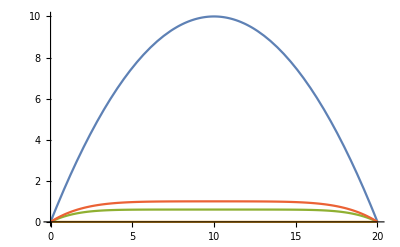

```mathematica
Plot[{v[x],u1[x],u2[x],u3[x]},{x,0,20}]
```

```mathematica
Plot3D[(-(x^2)/10)+2*x+Sum[(160*(Cos[n*Pi]-1)/((n*Pi)^3))*Exp[-((n*Pi/20)^2)*t]*Sin[n*Pi*x/20], {n,50}], {x,0,20},{t,0,100}, AxesLabel->Automatic]
```

-Graphics3D-

#### Problem 10.7.8ac

```mathematica
U[x_,t_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*t/10], {n,50}]
```

```mathematica
ux1[x_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*1/10], {n,50}]
```

```mathematica
ux2[x_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*3/10], {n,50}]
```

```mathematica
ux3[x_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*5/10], {n,50}]
```

```mathematica
ux4[x_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*12/10], {n,50}]
```

```mathematica
ux5[x_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*15/10], {n,50}]
```

```mathematica
ux6[x_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*19/10], {n,50}]
```

```mathematica
ut1[t_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*1/10]*Sin[n*Pi*t/10], {n,50}]
```

```mathematica
ut2[t_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*2/10]*Sin[n*Pi*t/10], {n,50}]
```

```mathematica
ut3[t_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*3/10]*Sin[n*Pi*t/10], {n,50}]
```

```mathematica
ut4[t_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*4/10]*Sin[n*Pi*t/10], {n,50}]
```

```mathematica
ut5[t_]:=Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*5/10]*Sin[n*Pi*t/10], {n,50}]
```

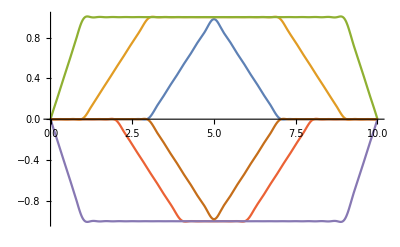

```mathematica
Plot[{ux1[x],ux2[x],ux3[x],ux4[x],ux5[x],ux6[x]},{x,0,10}]
```

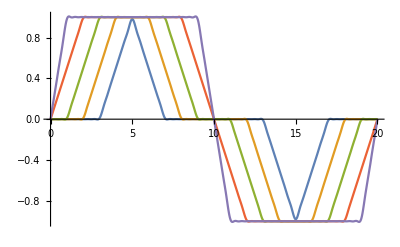

```mathematica
Plot[{ut1[t],ut2[t],ut3[t],ut4[t],ut5[t]},{t,0,20}]
```

```mathematica
Plot[Plot[{ux1[x],ux2[x],ux3[x]},{x,0,10}]
```

```mathematica
Plot3D[Sum[(40/((n*Pi)^2))*Sin[n*Pi/2]*Sin[n*Pi/10]*Sin[n*Pi*x/10]*Sin[n*Pi*t/10], {n,10}], {x,0,10},{t,0,20},PlotRange-> Full, AxesLabel->Automatic]
```

#### Problem 10.7.10bc

```mathematica
u[x_,t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

```mathematica
Plot3D[Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/25)*x], {n,100}], {x,0,10},{t,0,40},PlotRange-> Full,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
ux1[x_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*0]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

```mathematica
ux2[x_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*1]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

```mathematica
ux3[x_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*3]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

```mathematica
ux4[x_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*5]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

```mathematica
ux5[x_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*7]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

```mathematica
ux6[x_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*9]*Sin[(((2*n)-1)*Pi/20)*x], {n,50}]
```

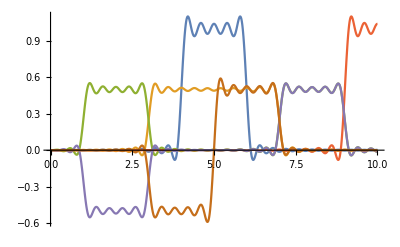

```mathematica
Plot[{ux1[x],ux2[x],ux3[x],ux4[x],ux5[x],ux6[x]},{x,0,10}]
```

```mathematica
ut1[t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*0], {n,50}]
```

```mathematica
ut2[t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*1], {n,50}]
```

```mathematica
ut3[t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*3], {n,50}]
```

```mathematica
ut4[t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*5], {n,50}]
```

```mathematica
ut5[t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*7], {n,50}]
```

```mathematica
ut6[t_]:=Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/20)*9], {n,50}]
```

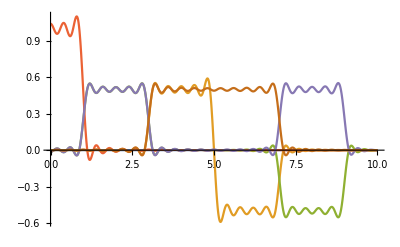

```mathematica
Plot[{ut1[t],ut2[t],ut3[t],ut4[t],ut5[t],ut6[t]},{t,0,10}]
```

```mathematica
Animate[Plot[Sum[(8/(((2*n)-1)*Pi))*Sin[((2*n)-1)*Pi/4]*Sin[((2*n)-1)*Pi/20]*Cos[(((2*n)-1)*Pi/20)*t]*Sin[(((2*n)-1)*Pi/25)*x], {n,50}], {x,0,10}, PlotRange-> {{0,10},{-2,2}}],{t,0,40}, DisplayAllSteps-> True,AnimationRunning-> False, RefreshRate-> 60]
```